# Angular Distribution of emission

```mathematica
(* Before radiation, the nucleus or atom has angular momentum J,M *)
Subscript[Φ, JM]
(* the emission radiation l,Subscript[m, l] *)
Subscript[ψ, Subscript[lm, l]]
(* the daugther j,m *)
Subscript[Φ, jm]
(* the wave function eqated by *)
Subscript[Φ, JM]=Subscript[Σψ, Subscript[lm, l]] Subscript[Φ, jm] CG[l,Subscript[m, l],j,m,J,M]
Subscript[ψ, Subscript[lm, l]]=A u[r]Y[l,Subscript[m, l]]
(* the probability of finding the emission at angle θ, ϕ *) 
<Subscript[ψ, Subscript[lm, l]]>
(* for fixed distance the integartion of spacial part is constant *)
(* The angular part does not need to integrate, because we need the angular distribution *)
<CG[l,Subscript[m, l],j,m,J,M]Y[l,Subscript[m, l]]>
```

```mathematica
Y[l_,m_,θ_,ϕ_]:=SphericalHarmonicY[l,m,θ,ϕ]
```

```mathematica
AmpY[l_,m_,θ_]:=SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l,m,θ,-ϕ]
```

```mathematica
AmpY[1,1,θ]
```

1/2 √(3/(2 π)) Sin[θ]

```mathematica
Manipulate[
Plot[Evaluate[Table[AmpY[j,m,θ],{m,0,j}]],{θ,-π,π},PlotStyle->Table[ColorData["Rainbow",If[j==0,1,1-m/j]],{m,0,j}],ImageSize->600],
{j,0,7,1}]
```

```mathematica
Manipulate[
Plot[Total[Table[AmpY[j,m,θ],{m,0,j}]]/(j+1),{θ,-π,π},ImageSize->600,PlotRange->{0,1}],
{j,0,7,1}]
```

```mathematica
CG[j_,m_,j1_,m1_,j2_,m2_]:=KroneckerDelta[m,m1+m2] Sqrt[((2 j+1) (j+j1-j2)! (j-j1+j2)! (j1+j2-j)!)/(j1+j2+j+1)!] Sqrt[(j+m)! (j-m)! (j1-m1)! (j1+m1)! (j2-m2)! (j2+m2)!]Sum[(-1)^k/(k! (j1+j2-j-k)! (j1-m1-k)! (j2+m2-k)! (j-j2+m1+k)! (j-j1-m2+k)!),{k,0,Min[j1+j2-j,j1-m1,j2+m2]}]
```

```mathematica
(* Combination *)
(* M= mj + m *)

Com[J_,M_,numl_,numj_]:=DeleteCases[Flatten[
Table[
If[And[-j≤ M-m≤ j,Abs[j-l]≤ J≤ j+l],{l,m,j,M-m},0]
,{l,0,numl},{m,-l,l},{j,0,numj}]
,2],0]
```

```mathematica
Com[1,1,3,2]
```

{{0,0,1,1},{1,-1,2,2},{1,0,1,1},{1,0,2,1},{1,1,0,0},{1,1,1,0},{1,1,2,0},{2,-1,2,2},{2,0,1,1},{2,0,2,1},{2,1,1,0},{2,1,2,0},{2,2,1,-1},{2,2,2,-1},{3,-1,2,2},{3,0,2,1},{3,1,2,0},{3,2,2,-1},{3,3,2,-2}}

```mathematica
Com[0,0,3,2]
```

{{0,0,0,0},{1,-1,1,1},{1,0,1,0},{1,1,1,-1},{2,-2,2,2},{2,-1,2,1},{2,0,2,0},{2,1,2,-1},{2,2,2,-2}}

```mathematica
Weighting[J_,M_,numl_,numj_]:=Flatten[
Table[
If[And[-j≤ M-m≤ j,Abs[j-l]≤ J≤ j+l],CG[J,M,l,m,j,M-m]^2,0]
,{l,0,numl},{m,-l,l},{j,0,numj}]
,2]
```

```mathematica
Com[0,0,2,2]
Weighting[0,0,2,2]
```

{{0,0,0,0},{1,-1,1,1},{1,0,1,0},{1,1,1,-1},{2,-2,2,2},{2,-1,2,1},{2,0,2,0},{2,1,2,-1},{2,2,2,-2}}

{1,0,0,0,1/3,0,0,1/3,0,0,1/3,0,0,0,1/5,0,0,1/5,0,0,1/5,0,0,1/5,0,0,1/5}

```mathematica
(* assume the radial part contribute the same for all angular momentum *)
AngDistri[J_,M_,num_,θ_]:=Total[Flatten[
Table[
If[And[-j≤ M-m≤ j,Abs[j-l]≤ J≤ j+l],CG[J,M,l,m,j,M-m]^2 AmpY[l,m,θ],0]
,{l,0,num},{m,-l,l},{j,0,num}]
,2]]//Simplify
```

```mathematica
Table[AngDistri[1,0,numl,0],{numl,0,4}]
```

{0,1/π,9/(5 π),18/(7 π),10/(3 π)}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{Indeterminate,1/8 (5+3 Cos[2 θ]),1/704 (499+140 Cos[2 θ]+65 Cos[4 θ]),(7937+1500 Cos[2 θ]+675 Cos[4 θ])/10112,(12475+1788 Cos[2 θ]+777 Cos[4 θ])/15040,(10029+1160 Cos[2 θ]+491 Cos[4 θ])/11680,(123295+11964 Cos[2 θ]+4965 Cos[4 θ])/140224}

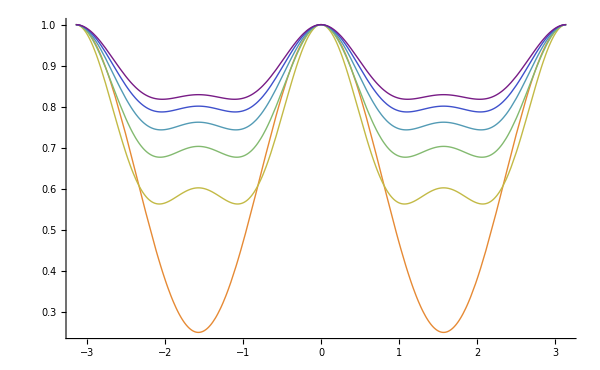

```mathematica
Table[AngDistri[2,0,numl,θ]/AngDistri[2,0,numl,0],{numl,0,6}]
Plot[%,{θ,-π,π},ImageSize->600,PlotRange->{0,All},PlotStyle->Table[ColorData["Rainbow",1-m],{m,0,1,1/6}]]
```

```mathematica
Manipulate[
Plot[Evaluate[Table[AmpY[j,m,θ],{m,0,j}]],{θ,-π,π},PlotStyle->Table[ColorData["Rainbow",If[j==0,1,1-m/j]],{m,0,j}],ImageSize->600,PlotRange->{0,1}],
{j,0,7,1}]
```

```mathematica
Manipulate[
Plot[Evaluate[Table[AmpY[j,m,θ],{j,0,m+6}]],{θ,-π,π},PlotStyle->Table[ColorData["Rainbow",If[m==0,1,1-j/(m+6)]],{j,0,m+6}],ImageSize->600,PlotRange->{0,1}],
{m,0,7,1}]
```